```mathematica
X[J_,μ_]:=1/2(J+μ);
B[J_]:= Exp[-J]
```

```mathematica
nm=13;
```

### Thermo limit

```mathematica
λm[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]-√(Sinh[X[J,μ]]^2+B[J]));
λp[J_,μ_]:=Exp[X[J,μ]](Cosh[X[J,μ]]+√(Sinh[X[J,μ]]^2+B[J]));
```

```mathematica
ξ[J_,μ_]:= Log[(λp[J,μ]/λm[J,μ])]^-1
```

```mathematica
vm[J_,μ_]:= Exp[-μ/2](λm[J,μ]-1);
```

```mathematica
ϕv[J_,μ_]:= 1/(1+vm[J,μ]^2);
```

```mathematica
ϕcorTL[J_,μ_,r_]:=1/((1+vm[J,μ]^2)^2)(1 + (λm[J,μ]/λp[J,μ])^r vm[J,μ]^2);
```

```mathematica
ϕTL[J_,μ_]:= 1/nm Sum[ϕv[J,μ],{i,1,nm}];
```

```mathematica
ϕv2[J_,μ_]:= 1/nm^2 Sum[ϕcorTL[J,μ,r],{r,1,nm},{i,1,nm}];
```

```mathematica
σTL[J_,μ_]:= Sqrt[ϕv2[J,μ]-ϕTL[J,μ]^2];
```

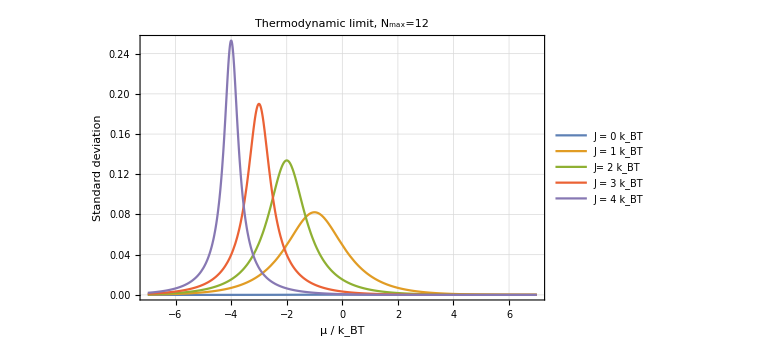

```mathematica
Plot[{σTL[0.00001,μ],σTL[1,μ],σTL[2,μ],σTL[3,μ],σTL[4,μ]},{μ,-7,7}, ImageSize->Large,PlotRange->Full,Frame->True,GridLines->Automatic,FrameLabel->{"μ / k_BT","Standard deviation"}, LabelStyle->{GrayLevel[0],12},PlotLegends->Placed[LineLegend[{"J = 0 k_BT","J = 1 k_BT","J= 2 k_BT","J = 3 k_BT","J = 4 k_BT"},LegendFunction->Frame],{{0.9,0.5},{0.7,0.5}}],PlotLabel->"Thermodynamic limit, N_max=12"]
```

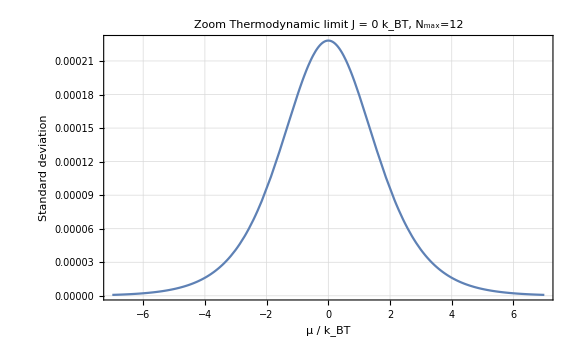

```mathematica
Plot[{σTL[0.00001,μ]},{μ,-7,7}, ImageSize->Large,PlotRange->Full,Frame->True,GridLines->Automatic,FrameLabel->{"μ / k_BT","Standard deviation"}, LabelStyle->{GrayLevel[0],12},PlotLabel->"Zoom Thermodynamic limit J = 0 k_BT, N_max=12"]
```

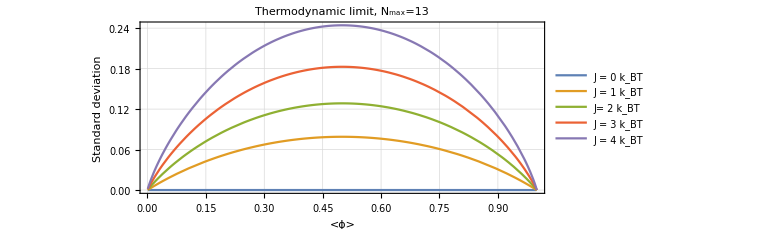

```mathematica
ParametricPlot[{{ϕv[0.0000001,μ],σTL[0.0000001,μ]},{ϕv[1,μ],σTL[1,μ]},{ϕv[2,μ],σTL[2,μ]},{ϕv[3,μ],σTL[3,μ]},{ϕv[4,μ],σTL[4,μ]}},{μ,-7,7},Frame->True,PlotRange->Full,GridLines->Automatic,ImageSize->Large,FrameLabel->{"<ϕ>","Standard deviation"},LabelStyle->{GrayLevel[0],12},PlotLegends -> LineLegend[{"J = 0 k_BT","J = 1 k_BT","J= 2 k_BT","J = 3 k_BT","J = 4 k_BT"},LegendFunction->Frame],PlotLabel->"Thermodynamic limit, N_max=13"]
```

```mathematica
Export["/home/mariajose/Escritorio/Mathematica/Plots/Standard deviation/Phi_vs_std_THEORY_TL.png",%30]
```

/home/mariajose/Escritorio/Mathematica/Plots/Standard deviation/Phi_vs_std_THEORY_TL.png

### Exact solution

```mathematica
ϕav[J_,μ_]:=(λp[J,μ]^nm+λm[J,μ]^nm vm[J,μ]^2)/((λp[J,μ]^nm+λm[J,μ]^nm)(1+vm[J,μ]^2));
```

```mathematica
ϕ[J_,μ_]:= 1/nm Sum[ϕav[J,μ],{i,1,nm}]
```

```mathematica
N[ϕ[0.000001,-2.5]]
```

0.0758582

```mathematica
ϕcor[J_,μ_,r_]:=(λp[J,μ]^nm(1+Exp[-r/ξ[J,μ]] vm[J,μ]^2)+λm[J,μ]^nm(Exp[r/ξ[J,μ]] vm[J,μ]^2+vm[J,μ]^4))/((λp[J,μ]^nm+λm[J,μ]^nm)(1+vm[J,μ]^2)^2)
```

```mathematica
ϕav2[J_,μ_]:= 1/nm^2 Sum[ϕcor[J,μ,r],{r,1,nm},{i,1,nm}]
```

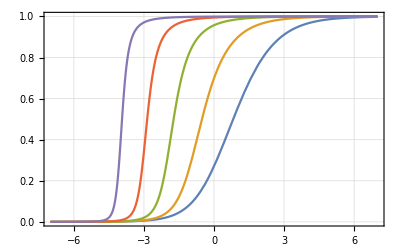

```mathematica
Plot[Evaluate[Table[ϕav2[J,μ],{J,0.000001,5}]],{μ,-7,7},Frame->True,GridLines->Automatic]
```

```mathematica
σ[J_,μ_]:= Sqrt[ϕav2[J,μ]-ϕ[J,μ]^2]
```

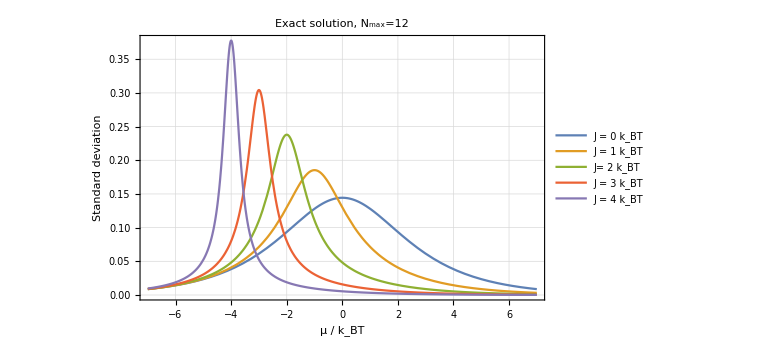

```mathematica
Plot[{σ[0.0000001,μ],σ[1,μ],σ[2,μ],σ[3,μ],σ[4,μ]},{μ,-7,7}, ImageSize->Large,PlotRange->Full,Frame->True,GridLines->Automatic,FrameLabel->{"μ / k_BT","Standard deviation"}, LabelStyle->{GrayLevel[0],12},PlotLegends->Placed[LineLegend[{"J = 0 k_BT","J = 1 k_BT","J= 2 k_BT","J = 3 k_BT","J = 4 k_BT"},LegendFunction->Frame],{{0.9,0.5},{0.7,0.5}}],PlotLabel->"Exact solution, N_max=12"]
```

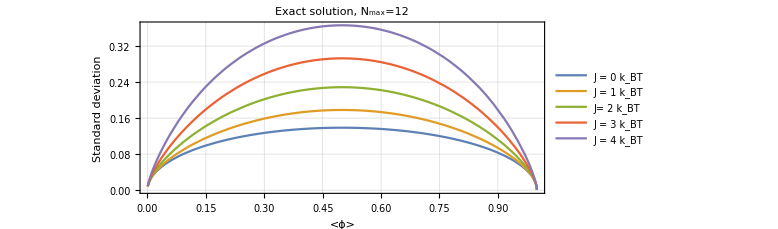

```mathematica
ParametricPlot[{{ϕ[0.0000001,μ],σ[0.0000001,μ]},{ϕ[1,μ],σ[1,μ]},{ϕ[2,μ],σ[2,μ]},{ϕ[3,μ],σ[3,μ]},{ϕ[4,μ],σ[4,μ]}},{μ,-7,7},Frame->True,PlotRange->Full,GridLines->Automatic,ImageSize->Large,FrameLabel->{"<ϕ>","Standard deviation"},LabelStyle->{GrayLevel[0],12},PlotLegends -> LineLegend[{"J = 0 k_BT","J = 1 k_BT","J= 2 k_BT","J = 3 k_BT","J = 4 k_BT"},LegendFunction->Frame],PlotLabel->"Exact solution, N_max=12"]
```

```mathematica
Export["/home/mariajose/Escritorio/Mathematica/Plots/Standard deviation/Phi_vs_std_THEORY.png",%22]
```

/home/mariajose/Escritorio/Mathematica/Plots/Standard deviation/Phi_vs_std_THEORY.png

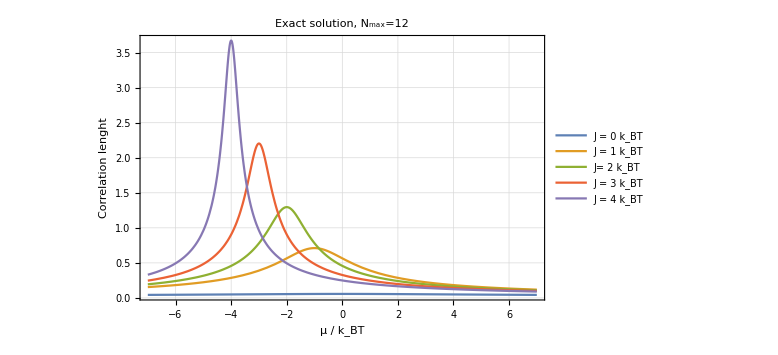

```mathematica
Plot[{ξ[0.0000001,μ],ξ[1,μ],ξ[2,μ],ξ[3,μ],ξ[4,μ]},{μ,-7,7}, ImageSize->Large,PlotRange->Full,Frame->True,GridLines->Automatic,FrameLabel->{"μ / k_BT","Correlation lenght"}, LabelStyle->{GrayLevel[0],12},PlotLegends->Placed[LineLegend[{"J = 0 k_BT","J = 1 k_BT","J= 2 k_BT","J = 3 k_BT","J = 4 k_BT"},LegendFunction->Frame],{{0.9,0.5},{0.7,0.5}}],PlotLabel->"Exact solution, N_max=12"]
```

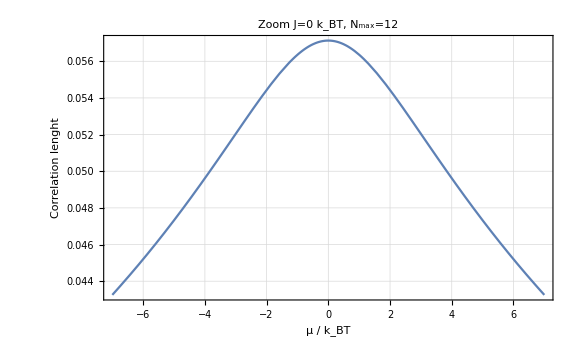

```mathematica
Plot[ξ[0.0000001,μ],{μ,-7,7}, ImageSize->Large,PlotRange->Full,Frame->True,GridLines->Automatic,FrameLabel->{"μ / k_BT","Correlation lenght"}, LabelStyle->{GrayLevel[0],12},PlotLabel->"Zoom J=0 k_BT, N_max=12"]
```

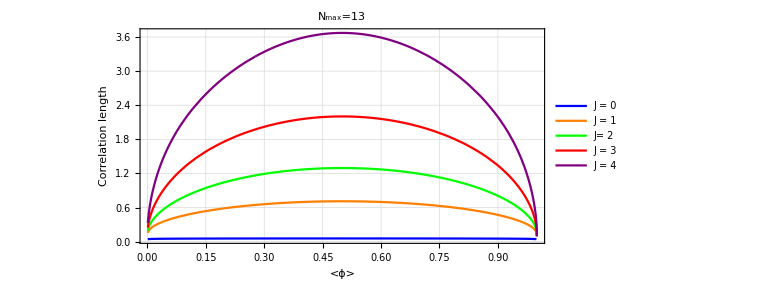

```mathematica
ParametricPlot[{{ϕav[0.0000001,μ],ξ[0.0000001,μ]},{ϕav[1,μ],ξ[1,μ]},{ϕav[2,μ],ξ[2,μ]},{ϕav[3,μ],ξ[3,μ]},{ϕav[4,μ],ξ[4,μ]}},{μ,-7,7},Frame->True,PlotRange->Full,GridLines->Automatic,ImageSize->Large,FrameLabel->{"<ϕ>","Correlation length"},LabelStyle->{GrayLevel[0],12},PlotLabel-> "N_max=13",PlotLegends -> LineLegend[{"J = 0","J = 1","J= 2","J = 3","J = 4"},LegendFunction->Frame],AspectRatio->1/2,PlotStyle->{{Blue},{Orange},{Green},{Red},{Purple}}]
```

```mathematica
Limit[ξ[J,-J],J-> Infinity]
```

∞

```mathematica
Export["/home/mariajose/Escritorio/Mathematica/Plots/Standard deviation/CorrLength_vs_phi.png",%54]
```

/home/mariajose/Escritorio/Mathematica/Plots/Standard deviation/CorrLength_vs_phi.png

```mathematica
Needs["ErrorBarPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Data0 = Import["/media/luke/Elements/Simulations/Without _depletion/Glauber/Std_vs_Nss/sdt_vs_Nss_J=0_Res.dat"];
Data1 = Import["/media/luke/Elements/Simulations/Without _depletion/Glauber/Std_vs_Nss/sdt_vs_Nss_J=1_Res.dat"];
Data2 = Import["/media/luke/Elements/Simulations/Without _depletion/Glauber/Std_vs_Nss/sdt_vs_Nss_J=2_Res.dat"];
Data3 = Import["/media/luke/Elements/Simulations/Without _depletion/Glauber/Std_vs_Nss/sdt_vs_Nss_J=3_Res.dat"];
Data4 = Import["/media/luke/Elements/Simulations/Without _depletion/Glauber/Std_vs_Nss/sdt_vs_Nss_J=4_Res.dat"];
```

```mathematica
Data0kmc = Import["/media/luke/Elements/Simulations/Without _depletion/KMC/CooperativityKMC/Equilibrium_analysis/sdt_vs_Nss_J=0_Res.dat"];
Data1kmc = Import["/media/luke/Elements/Simulations/Without _depletion/KMC/CooperativityKMC/Equilibrium_analysis/sdt_vs_Nss_J=1_Res.dat"];
Data2kmc = Import["/media/luke/Elements/Simulations/Without _depletion/KMC/CooperativityKMC/Equilibrium_analysis/sdt_vs_Nss_J=2_Res.dat"];
Data3kmc = Import["/media/luke/Elements/Simulations/Without _depletion/KMC/CooperativityKMC/Equilibrium_analysis/sdt_vs_Nss_J=3_Res.dat"];
Data4kmc = Import["/media/luke/Elements/Simulations/Without _depletion/KMC/CooperativityKMC/Equilibrium_analysis/sdt_vs_Nss_J=4_Res.dat"];
```

Import::nffil: File /home/mariajose/Escritorio/Simulations/Without _depletion/Glauber/SS_Stall.dat not found during Import.

```mathematica
Data0kmcB = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=0_a= 3.06_Res.dat"];
Data1kmcB = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=0_a= 6.15_Res.dat"];
Data2kmcB = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=0_a=30.44_Res.dat"];
Data0kmcB1 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=1_a= 3.06_Res.dat"];
Data1kmcB1 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=1_a= 6.15_Res.dat"];
Data2kmcB1 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=1_a=30.44_Res.dat"];
Data0kmcB2 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=2_a= 3.06_Res.dat"];
Data1kmcB2 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=2_a= 6.15_Res.dat"];
Data2kmcB2 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=2_a=30.44_Res.dat"];
Data0kmcB3 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=3_a= 3.06_Res.dat"];
Data1kmcB3 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=3_a= 6.15_Res.dat"];
Data2kmcB3 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=3_a=30.44_Res.dat"];
Data0kmcB4 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=4_a= 3.06_Res.dat"];
Data1kmcB4 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=4_a= 6.15_Res.dat"];
Data2kmcB4 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=4_a=30.44_Res.dat"];
```

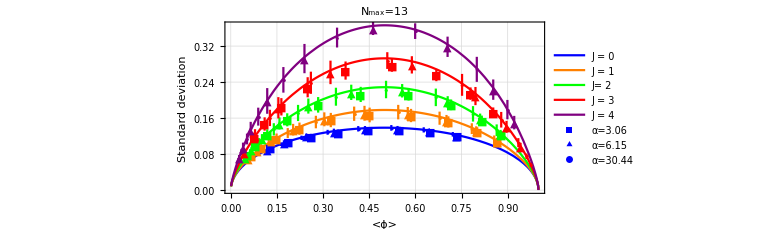

```mathematica
Show[ParametricPlot[{{ϕav[0.0000001,μ],σ[0.0000001,μ]},{ϕav[1,μ],σ[1,μ]},{ϕav[2,μ],σ[2,μ]},{ϕav[3,μ],σ[3,μ]},{ϕav[4,μ],σ[4,μ]}},{μ,-7,7},ImageSize->Large,PlotRange->Full,Frame-> True,GridLines-> Automatic, PlotLegends -> LineLegend[{"J = 0","J = 1","J= 2","J = 3","J = 4"},LegendFunction->Framed], FrameLabel->{"<ϕ>","Standard deviation"},LabelStyle->{GrayLevel[0],12},PlotStyle->{{Blue},{Orange},{Green},{Red},{Purple}},PlotLabel->"N_max=13"],ErrorListPlot[{Data0kmcB[[All,{3,4,5}]]/nm,Data1kmcB[[All,{3,4,5}]]/nm,Data2kmcB[[All,{3,4,5}]]/nm,Data0kmcB1[[All,{2,3,4}]]/nm,Data1kmcB1[[All,{2,3,4}]]/nm,Data2kmcB1[[All,{2,3,4}]]/nm,Data0kmcB2[[All,{2,3,4}]]/nm,Data1kmcB2[[All,{2,3,4}]]/nm,Data2kmcB2[[All,{2,3,4}]]/nm,Data0kmcB3[[All,{2,3,4}]]/nm,Data1kmcB3[[All,{2,3,4}]]/nm,Data2kmcB3[[All,{2,3,4}]]/nm,Data0kmcB4[[All,{2,3,4}]]/nm,Data1kmcB4[[All,{2,3,4}]]/nm,Data2kmcB4[[All,{2,3,4}]]/nm}, PlotMarkers->{Style["■",Blue],Style["▲",Blue],Style["•",Blue],Style["■",Orange],Style["▲",Orange],Style["•",Orange],Style["■",Green],Style["▲",Green],Style["•",Green],Style["■",Red],Style["▲",Red],Style["•",Red],Style["■",Purple],Style["▲",Purple],Style["•",Purple]},PlotStyle->{Blue,Blue,Blue,Orange,Orange,Orange,Green,Green,Green,Red,Red,Red,Purple,Purple,Purple},PlotLegends->LineLegend[{"α=3.06","α=6.15","α=30.44"},LegendFunction->Framed]]]
```

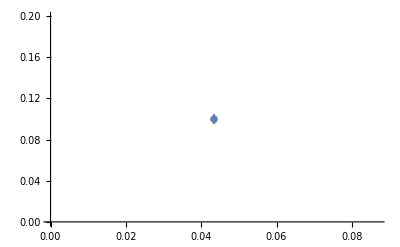

```mathematica
ErrorListPlot[Data0kmcB4[[All,{3,4,5}]]/nm,PlotRange->Full]
```

```mathematica
Export["/home/mariajose/Escritorio/Mathematica/Plots/Standard deviation/Std_vs_phi_TH_SIM_Resurrection.png",%31]
```

/home/mariajose/Escritorio/Mathematica/Plots/Standard deviation/Std_vs_phi_TH_SIM_Resurrection.png

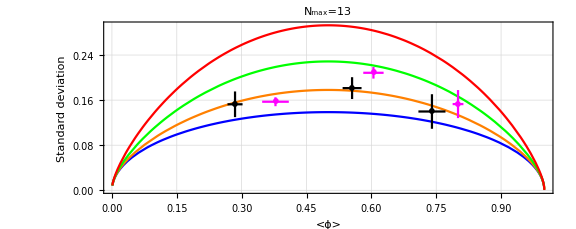

```mathematica
plot=Show[ParametricPlot[{{ϕav[0.0000001,μ],σ[0.0000001,μ]},{ϕav[1,μ],σ[1,μ]},{ϕav[2,μ],σ[2,μ]},{ϕav[3,μ],σ[3,μ]}},{μ,-7,7},ImageSize->Large,PlotRange->Full,Frame-> True,GridLines-> Automatic,  FrameLabel->{"<ϕ>","Standard deviation"},LabelStyle->{GrayLevel[0],12},PlotStyle->{{Blue},{Orange},{Green},{Red}},PlotLabel->"N_max=13"],ErrorListPlot[{{{#1,#2},ErrorBarPlots`ErrorBar@@{#4,#3}}&@@@Data5,{{#1,#2},ErrorBarPlots`ErrorBar@@{#4,#3}}&@@@Data6},PlotMarkers->{Style["•",20,Black],Style["•",20,Magenta]},PlotStyle-> {Black,Magenta}]]
```

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

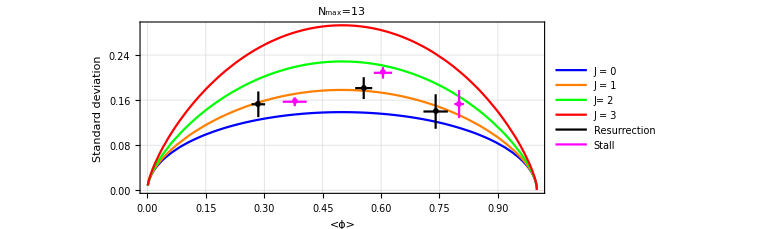

```mathematica
Legended[plot,LineLegend[{Blue,Orange,Green,Red,Black, Magenta},{"J = 0","J = 1","J= 2","J = 3","Resurrection","Stall"},LegendFunction->Frame]]
```

```mathematica
Export["/home/mariajose/Escritorio/Mathematica/Plots/Standard deviation/Std_vs_phi_EXP.png",%33]
```

/home/mariajose/Escritorio/Mathematica/Plots/Standard deviation/Std_vs_phi_EXP.png

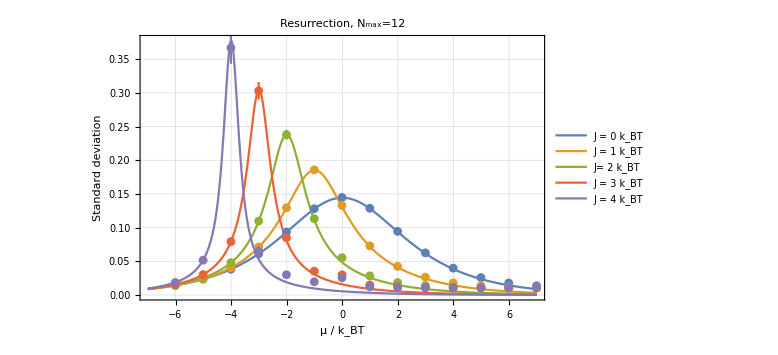

```mathematica
Show[Plot[{σ[0.0000001,μ],σ[1,μ],σ[2,μ],σ[3,μ],σ[4,μ]},{μ,-7,7}, ImageSize->Large,PlotRange->Full,Frame->True,GridLines->Automatic,FrameLabel->{"μ / k_BT","Standard deviation"}, LabelStyle->{GrayLevel[0],12},PlotLegends->Placed[LineLegend[{"J = 0 k_BT","J = 1 k_BT","J= 2 k_BT","J = 3 k_BT","J = 4 k_BT"},LegendFunction->Frame],{{0.9,0.5},{0.7,0.5}}],PlotLabel->"Resurrection, N_max=12"],ErrorListPlot[{Data0[[All,{1,3,4}]],Data1[[All,{1,3,4}]],Data2[[All,{1,3,4}]],Data3[[All,{1,3,4}]],Data4[[All,{1,3,4}]]}]]
```